```mathematica
Clear[ω]
```

```mathematica
Clear["Global`*"]
```

```mathematica
J=1;
γ[kx_,ky_]:=1/2*(Cos[kx]+Cos[ky]);
ω[kx_,ky_,b_]:=Sqrt[A[kx,ky,b]^2-B[kx,ky,b]^2];
ϵ[kx_,ky_,b_]:=2*J*ω[kx,ky,b];
A[kx_,ky_,b_]:=1+γ[kx,ky]*b^2;
B[kx_,ky_,b_]:=γ[kx,ky]*(1-b^2);
u[kx_,ky_,b_]:=Sqrt[(A[kx,ky,b]+ω[kx,ky,b])/(2*ω[kx,ky,b])];
v[kx_,ky_,b_]:=Sinh[ArcTanh[B[kx,ky,b]/A[kx,ky,b]]/2];
```

```mathematica
Manipulate[DensityPlot[u[x,y,b],{x,-π,π},{y,-π,π}],{b,0,1}]
```

```mathematica
Manipulate[DensityPlot[v[x,y,b],{x,-π,π},{y,-π,π}],{b,0,1}]
```

```mathematica
Manipulate[Plot[{u[x,x,b],v[x,x,b]},{x,-π,π}],{b,0,1,0.05}]
```

```mathematica
Φ1[kx_,ky_,qx_,qy_,b_]:=1/2*(γ[kx,ky]*(u[kx,ky,b]+v[kx,ky,b])*(u[qx,qy,b]*v[kx-qx+π,ky-qy+π,b]+v[qx,qy,b]*u[kx-qx+π,ky-qy+π,b])+γ[qx,qy]*(u[qx,qy,b]+v[qx,qy,b])*(u[kx,ky,b]*v[kx-qx+π,ky-qy+π,b]+v[kx,ky,b]*u[kx-qx+π,ky-qy+π,b])+γ[kx-qx+π,ky-qy+π]*(u[kx-qx+π,ky-qy+π,b]+v[kx-qx+π,ky-qy+π,b])*(u[qx,qy,b]*v[kx,ky,b]+v[qx,qy,b]*u[kx,ky,b]));
```

```mathematica
e=0.01;
Manipulate[DensityPlot[Φ1[x,y,qx,qy,b]^2/e/(π^2*((ϵ[x,y,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,y-qy+π,b])^2+e^2)),{qx,0.1π,π-0.1π},{qy,0.1π,π-0.1π},PlotLegends->Automatic,PlotRange->All],{x,0,π},{y,0,π},{b,0.01,1}]
```

```mathematica
Φ1[49/50*π,49/50*π,49/50*π,49/50*π,0.1]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Indeterminate

```mathematica
test=ParallelTable[Table[{b,4*NIntegrate[(Φ1[x,x,qx,qy,b])^2,{qx,0,π},{qy,0,π},MinRecursion->1,MaxRecursion->15,AccuracyGoal->5]},{b,0.01,1,0.01}],{x,0,π,1/10*π}];
```

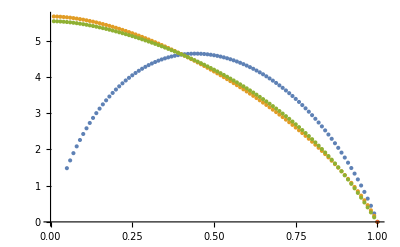

```mathematica
ListPlot[test]
```

```mathematica
kx=1;
ky=2;
b=8/10;
e=1/100;
NIntegrate[Φ1[kx,ky,qx,qy,b]^2*e/(π^2*((ϵ[kx,ky,b]-ϵ[qx,qy,b]-ϵ[kx-qx+π,ky-qy+π,b])^2+e^2)),{qx,0,π},{qy,0,π},MinRecursion->4,MaxRecursion->20,AccuracyGoal->5]
```

0.00909313

```mathematica
b=8/10;
testlist=ParallelTable[{x,1/(π^2)*NIntegrate[Φ1[x,x,qx,qy,b]^2*e/(((ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])^2+e^2)),{qx,0,π},{qy,0,π},MinRecursion->4,MaxRecursion->20,WorkingPrecision->10,AccuracyGoal->5]},{x,0,π-e*π,1/100*π}];
```

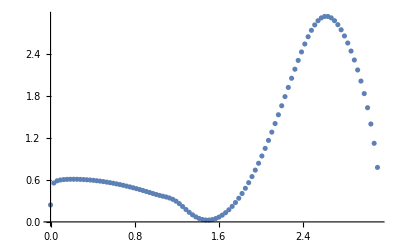

```mathematica
ListPlot[testlist]
```

```mathematica
x=1/2*π;
1/π^2*NIntegrate[Φ1[x,x,qx,qy,b]^2*(ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])/(((ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])^2+e^2)),{qx,0,π},{qy,0,π},MinRecursion->4,MaxRecursion->20]
```

0.00831945

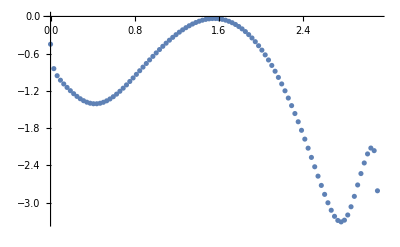

```mathematica
e=1/100;
b=1/10;
energycorrection=ParallelTable[{x,1/π^2*NIntegrate[Φ1[x,x,qx,qy,b]^2*(ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])/(((ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])^2+e^2)),{qx,0,π},{qy,0,π},MinRecursion->40,MaxRecursion->200]},{x,0,π-e*π,1/100*π}];
ListPlot[energycorrection]
```

```mathematica
b=0.9;
kx=0.2*π;
ky=0.5*π;
e=0.01;
testlist=Table[{x,NIntegrate[1/(2*π)*(Φ1[x,x,qx,qy,b])^2*e/((ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])^2+e^2),{qx,0,π},{qy,0,π},MinRecursion->40,MaxRecursion->50,WorkingPrecision->10]},{x,0,π,1/10*π}];
```

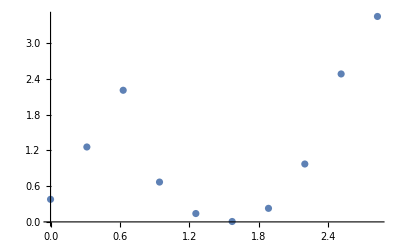

```mathematica
ListPlot[testlist]
```

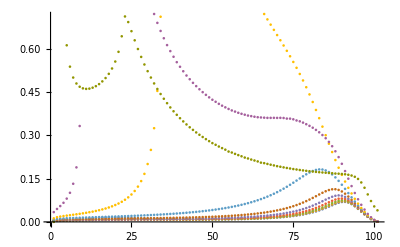

```mathematica
e=1/100;
testlist=Table[Table[NIntegrate[1/(π^2)*e/((ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])^2+e^2),{qx,0,π},{qy,0,π},Exclusions->{ϵ[qx,qy,b]+ϵ[x-qx+π,x-qy+π,b]==ϵ[x,x,b]},MinRecursion->400,MaxRecursion->500,AccuracyGoal->5,WorkingPrecision->10,Method->{GlobalAdaptive,MaxErrorIncreases->10000}],{x,0,π,1/100*π}],{b,0.1,1,1/10}];
ListPlot[testlist]
```

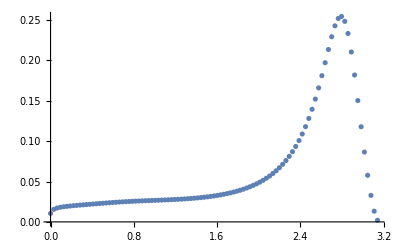

```mathematica
e=1/100;
b=4/10;
testlist=ParallelTable[{x,NIntegrate[1/(π^2)*e/((ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])^2+e^2),{qx,0,π},{qy,0,π},Exclusions->{ϵ[qx,qy,b]+ϵ[x-qx+π,x-qy+π,b]==ϵ[x,x,b]},MinRecursion->4,MaxRecursion->50,AccuracyGoal->5]},{x,0,π,1/100*π}];
ListPlot[testlist]
```

## energy correction

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,0.0981748},{0.,0.0981748}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,0.0981748},{0.,0.0981748}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,0.0981748},{0.,0.0981748}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,0.0981748},{0.,0.0981748}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,0.0981748},{0.,0.0981748}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,0.0981748},{0.,0.0981748}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,0.0981748},{0.,0.0981748}}.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0187816 and 7.58569×10^-6 for the integral and error estimates.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,0.0981748},{0.,0.0981748}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,0.0981748},{0.,0.0981748}}.

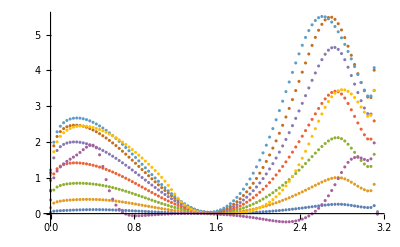

```mathematica
e=1/100;
b=1/10;
energycorrection=ParallelTable[Table[{x,-1/(π^2)*NIntegrate[8*J^2*b^2*(1-b^2)*Φ1[x,x,qx,qy,b]^2*(ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])/(((ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])^2+e^2)),{qx,0,π},{qy,0,π},MinRecursion->40,MaxRecursion->200]},{x,0,π,1/200*π}],{b,1/10,9/10,1/10}];
ListPlot[energycorrection]
```

## lifetime

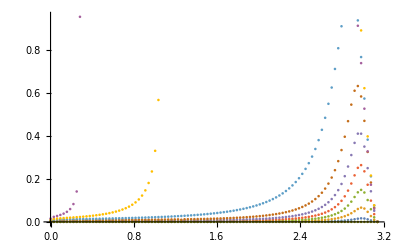

```mathematica
e=1/1000;
testlist=ParallelTable[Table[{x,NIntegrate[8*J^2*b^2*(1-b^2)/(π^2)*e/((ϵ[x,x,b]-ϵ[qx,qy,b]-ϵ[x-qx+π,x-qy+π,b])^2+e^2),{qx,0,π},{qy,0,π},MinRecursion->400,MaxRecursion->500,AccuracyGoal->5,WorkingPrecision->16]},{x,0,π,1/100*π}],{b,1/10,1,1/10}];
ListPlot[testlist]
```

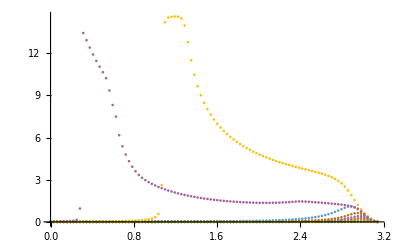

```mathematica
ListPlot[testlist,PlotRange->All]
```

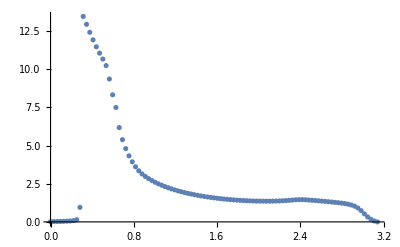

```mathematica
ListPlot[testlist[[9]],PlotRange->All]
```